This Notebook imports .dat files (for local Chern number on the middle line of a projected brane). Then it plots the local Chern number on every site.

The dat files imported in this notebook are generated by Local_Chern_Number_QAHI_projected_Brane.nb

```mathematica
Lx = 100;
Ly=100;
```

```mathematica
LineChernListP1 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m=6Xup=22Xdn=12PartsPerThousand=103Rational.dat"];
```

```mathematica
LineChernListP2 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m=2Xup=22Xdn=12PartsPerThousand=103Rational.dat"];
```

```mathematica
list1 = Table[LineChernListP1[[ii]][[3]],{ii,1,Lx}]
```

{-30.1807,0.985854,0.99612,0.998884,0.999504,0.999636,0.999691,0.999696,0.999667,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999667,0.999691,0.999673,0.999489,0.998869,0.996164,0.986019,-30.1731}

```mathematica
list2 = Table[LineChernListP2[[ii]][[3]],{ii,1,Lx}]
```

{30.1807,-0.985854,-0.99612,-0.998884,-0.999504,-0.999636,-0.999691,-0.999696,-0.999667,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999667,-0.999691,-0.999673,-0.999489,-0.998869,-0.996164,-0.986019,30.1731}

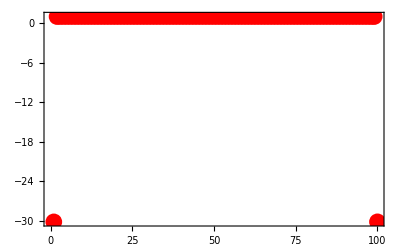

```mathematica
ListPlot[list1,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

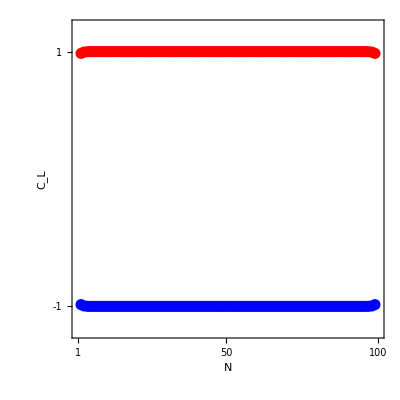

```mathematica
Show[ListPlot[list1,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","C_L"},RotateLabel->False]
```